```mathematica
p3k1train={-2.92989451,-2.83678806,-2.50461608,-1.900743,-1.37579921,-0.98199126,-0.81481943,-0.77649746,-0.77349145,-0.77393467,-0.76667596,-0.72870617,-0.64515339,-0.56852398,-0.54118823,-0.52709211,-0.51969359,-0.51685479,-0.51489232,-0.51085785,-0.5132751,-0.51131549,-0.5101967,-0.51120482,-0.51050632,-0.51036026,-0.51004417,-0.51042213,-0.51015532,-0.5082924};
```

```mathematica
p3k2train = 0.5*(p3k3train+p3k1train)
```

{-2.40146,-2.30084,-2.03808,-1.61246,-1.23212,-0.935502,-0.783834,-0.714994,-0.675309,-0.651941,-0.634837,-0.607439,-0.559917,-0.517031,-0.50029,-0.492686,-0.489198,-0.486449,-0.485841,-0.485246,-0.486397,-0.48691,-0.487358,-0.488469,-0.488817,-0.489892,-0.489224,-0.489475,-0.489395,-0.489633}

```mathematica
p3k3train={-1.87301915,-1.76489345,-1.57155267,-1.32417985,-1.08844113,-0.88901292,-0.75284819,-0.65349083,-0.57712603,-0.52994807,-0.5029985,-0.48617249,-0.47468069,-0.46553827,-0.45939201,-0.45828055,-0.45870224,-0.456044,-0.45678931,-0.45963376,-0.45951965,-0.46250411,-0.46451916,-0.46573222,-0.46712859,-0.46942294,-0.46840339,-0.46852865,-0.46863526,-0.47097289};
```

```mathematica
p3k4train = 0.5*(p3k3train+p3k5train)
```

{-1.61782,-1.55443,-1.44405,-1.29597,-1.14098,-0.990229,-0.858002,-0.740515,-0.641351,-0.570263,-0.524811,-0.496877,-0.477527,-0.464748,-0.455181,-0.452368,-0.451594,-0.448804,-0.449542,-0.451908,-0.454264,-0.456682,-0.459409,-0.461062,-0.463767,-0.463892,-0.464469,-0.466097,-0.465067,-0.467044}

```mathematica
p3k5train={-1.36262951,-1.34397591,-1.31655159,-1.26776815,-1.19351621,-1.09144421,-0.96315584,-0.82753978,-0.70557552,-0.61057702,-0.54662304,-0.50758099,-0.48037385,-0.46395842,-0.45096987,-0.44645521,-0.44448527,-0.44156428,-0.44229481,-0.44418139,-0.44900907,-0.45086079,-0.45429957,-0.45639133,-0.46040491,-0.4583603,-0.46053433,-0.46366617,-0.46149931,-0.46311484};
```

```mathematica
p3k6train = 0.5*(p3k5train+p3k7train)
```

{-1.18736,-1.16979,-1.14686,-1.10847,-1.05505,-0.981813,-0.890628,-0.792711,-0.703863,-0.625499,-0.564743,-0.52122,-0.487994,-0.466141,-0.452227,-0.444992,-0.439644,-0.437631,-0.436389,-0.437184,-0.440354,-0.443072,-0.44668,-0.449885,-0.452947,-0.453543,-0.457651,-0.458961,-0.458041,-0.459604}

```mathematica
p3k7train={-1.01209447,-0.99561333,-0.9771659,-0.94917494,-0.91657549,-0.87218094,-0.81809937,-0.75788253,-0.70215032,-0.6404201,-0.58286387,-0.5348581,-0.49561475,-0.46832365,-0.45348388,-0.44352948,-0.43480269,-0.43369829,-0.4304828,-0.43018615,-0.43169947,-0.43528244,-0.43906053,-0.4433795,-0.44548972,-0.4487253,-0.45476765,-0.45425538,-0.45458327,-0.45609407};
```

```mathematica
p3k8train = 0.5*(p3k7train+p3k9train)
```

{-0.894468,-0.882905,-0.86792,-0.847019,-0.823409,-0.789661,-0.748816,-0.703523,-0.659187,-0.6122,-0.566595,-0.525155,-0.493728,-0.470822,-0.456044,-0.446185,-0.435206,-0.430855,-0.429296,-0.426634,-0.427573,-0.431924,-0.435881,-0.439002,-0.443237,-0.445652,-0.451442,-0.452604,-0.453241,-0.454179}

```mathematica
p3k9train={-0.77684067,-0.77019764,-0.75867359,-0.74486215,-0.73024262,-0.70714059,-0.67953236,-0.64916269,-0.61622401,-0.58397935,-0.55032573,-0.51545151,-0.49184219,-0.47331954,-0.45860374,-0.4488403,-0.43560877,-0.42801195,-0.4281099,-0.42308151,-0.42344682,-0.42856514,-0.43270159,-0.43462497,-0.44098507,-0.4425788,-0.44811648,-0.45095242,-0.45189942,-0.45226359};
```

```mathematica
p3k10train = p3k9train+0.01
```

{-0.766841,-0.760198,-0.748674,-0.734862,-0.720243,-0.697141,-0.669532,-0.639163,-0.606224,-0.573979,-0.540326,-0.505452,-0.481842,-0.46332,-0.448604,-0.43884,-0.425609,-0.418012,-0.41811,-0.413082,-0.413447,-0.418565,-0.422702,-0.424625,-0.430985,-0.432579,-0.438116,-0.440952,-0.441899,-0.442264}

```mathematica
?Table
```

Table[expr,n] generates a list of n copies of expr. 
Table[expr,{i,i_max}] generates a list of the values of expr when i runs from 1 to i_max. 
Table[expr,{i,i_min,i_max}] starts with i=i_min. 
Table[expr,{i,i_min,i_max,di}] uses steps di. 
Table[expr,{i,{i_1,i_2,…}}] uses the successive values i_1, i_2, ….
Table[expr,{i,i_min,i_max},{j,j_min,j_max},…] gives a nested list. The list associated with i is outermost.

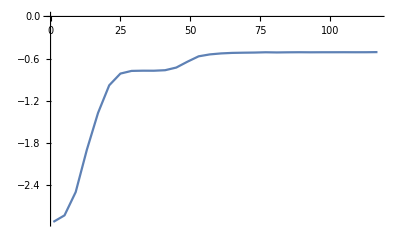

```mathematica
ListLinePlot[Table[{4*(i-1)+1,p3k1train[[i]]},{i,1,Length[p3k1train]}]]
```

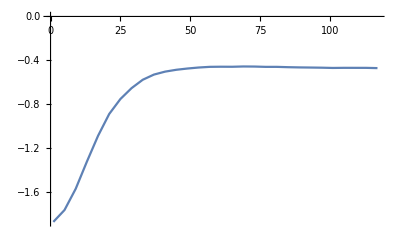

```mathematica
ListLinePlot[Table[{4*(i-1)+1,p3k3train[[i]]},{i,1,Length[p3k1train]}]]
```

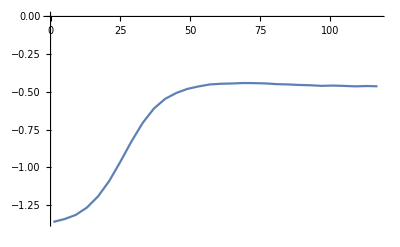

```mathematica
ListLinePlot[Table[{4*(i-1)+1,p3k5train[[i]]},{i,1,Length[p3k1train]}]]
```

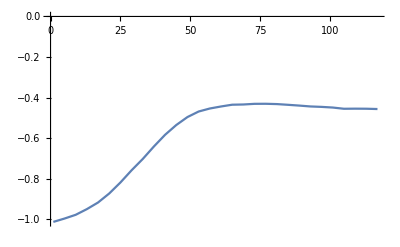

```mathematica
ListLinePlot[Table[{4*(i-1)+1,p3k7train[[i]]},{i,1,Length[p3k1train]}]]
```

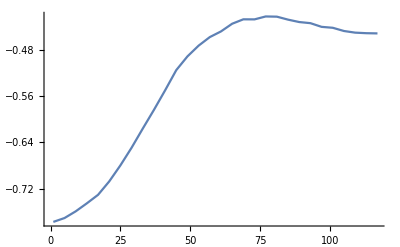

```mathematica
ListLinePlot[Table[{4*(i-1)+1,p3k9train[[i]]},{i,1,Length[p3k1train]}]]
```

```mathematica
(*trainlogliks/173073*)
```

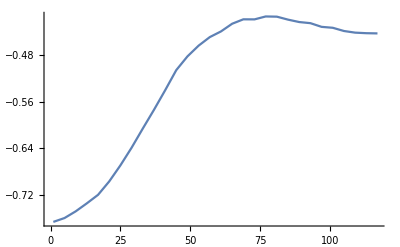

```mathematica
ListLinePlot[Table[{4*(i-1)+1,p3k10train[[i]]},{i,1,Length[p3k1train]}]]
```

```mathematica
p3k1test={-7.90834562,-6.90946421,-6.09654404,-5.60147299,-4.4932263,-3.02229543,-2.81810367,-2.62628346,-2.52732909,-2.25711244,-2.030647,-1.68755148,-1.39782947,-1.16317225,-0.96015269,-0.89192607,-0.8595143,-0.85361058,-0.83656328,-0.83469611,-0.831821,-0.82394126,-0.82319587,-0.830559,-0.83596907,-0.82076855,-0.83366577,-0.81935808,-0.82521571,-0.80387673};
```

```mathematica
p3k2test = 0.5*(p3k1test+p3k3test)
```

{-15.7092,-13.3737,-11.6602,-9.84289,-8.13691,-6.28853,-5.42723,-4.61627,-3.80366,-3.15605,-2.75116,-2.2448,-1.83786,-1.55198,-1.3303,-1.18163,-1.07319,-1.00647,-0.948022,-0.921067,-0.885554,-0.877653,-0.856236,-0.856444,-0.858368,-0.85109,-0.850681,-0.846921,-0.842895,-0.835667}

```mathematica
p3k3test={-23.51002951,-19.83786692,-17.22390387,-14.08429832,-11.7805844,-9.55477105,-8.03636449,-6.60625379,-5.07998502,-4.05497967,-3.47167084,-2.80205119,-2.27788059,-1.94078473,-1.70043913,-1.47133984,-1.28686153,-1.15932198,-1.05947974,-1.00743781,-0.93928788,-0.93136503,-0.88927514,-0.88232964,-0.8807674,-0.88141237,-0.86769697,-0.87448446,-0.86057372,-0.86745722};
```

```mathematica
p3k4test = 0.5*(p3k3test+p3k5test)
```

{-46.5183,-36.8521,-31.4854,-25.9613,-22.02,-17.8276,-15.2112,-11.5782,-9.29924,-7.3874,-6.27488,-4.70967,-3.90228,-3.12637,-2.45859,-2.02558,-1.66322,-1.4268,-1.23008,-1.11477,-1.02604,-0.985863,-0.929048,-0.913337,-0.905482,-0.897656,-0.879782,-0.880092,-0.875338,-0.872311}

```mathematica
p3k5test={-69.52658103,-53.86635477,-45.74680394,-37.83823929,-32.25933893,-26.10052813,-22.38608996,-16.55009456,-13.51849269,-10.71981112,-9.07809202,-6.61728863,-5.52667505,-4.31195158,-3.21675015,-2.57981374,-2.03958102,-1.69427702,-1.40068016,-1.22209392,-1.11280208,-1.04036159,-0.9688203,-0.94434486,-0.93019698,-0.91389992,-0.89186693,-0.88569889,-0.8901023,-0.87716434};
```

```mathematica
p3k6test = 0.5*(p3k5test+p3k7test)
```

{-91.3027,-71.503,-59.9605,-48.5264,-40.5153,-32.8581,-27.9258,-21.767,-17.8384,-14.2472,-11.5022,-8.943,-7.05301,-5.58012,-4.21426,-3.31837,-2.5736,-2.06641,-1.65663,-1.40078,-1.22472,-1.11918,-1.02623,-0.978031,-0.955467,-0.937081,-0.909944,-0.897974,-0.903012,-0.903815}

```mathematica
p3k7test={-113.07876663,-89.13968571,-74.1742933,-59.21461302,-48.77119642,-39.61559932,-33.46545208,-26.98380841,-22.15838143,-17.77449725,-13.92640031,-11.26871778,-8.57933772,-6.84829556,-5.21176133,-4.05692731,-3.10761242,-2.43853811,-1.91256995,-1.57947059,-1.33664424,-1.1979953,-1.08364188,-1.01171663,-0.98073769,-0.96026122,-0.92802075,-0.91024963,-0.91592146,-0.93046633};
```

```mathematica
p3k8test = 0.5*(p3k7test+p3k9test)
```

{-142.422,-110.077,-92.0966,-73.9278,-59.8888,-49.0744,-40.8643,-33.2202,-27.225,-21.7228,-17.1046,-13.839,-10.6505,-8.36612,-6.32998,-4.97114,-3.77345,-2.88691,-2.24007,-1.80168,-1.46619,-1.25994,-1.12711,-1.04743,-0.995459,-0.967539,-0.936612,-0.918897,-0.918835,-0.926284}

```mathematica
p3k9test={-171.76432378,-131.01387905,-110.01891259,-88.64089244,-71.00645028,-58.53326571,-48.26322423,-39.45649981,-32.29153614,-25.67119109,-20.28273549,-16.40927617,-12.72159101,-9.88393782,-7.44819082,-5.88535965,-4.43929106,-3.33527472,-2.56757359,-2.02389024,-1.59572595,-1.32188952,-1.17058586,-1.08313827,-1.01018018,-0.97481753,-0.9452029,-0.92754413,-0.92174785,-0.92210256};
```

```mathematica
p3k10test = p3k9test*1.1
```

{-188.941,-144.115,-121.021,-97.505,-78.1071,-64.3866,-53.0895,-43.4021,-35.5207,-28.2383,-22.311,-18.0502,-13.9938,-10.8723,-8.19301,-6.4739,-4.88322,-3.6688,-2.82433,-2.22628,-1.7553,-1.45408,-1.28764,-1.19145,-1.1112,-1.0723,-1.03972,-1.0203,-1.01392,-1.01431}

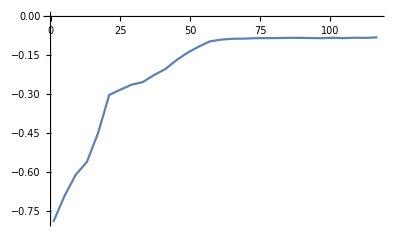

```mathematica
ListLinePlot[Table[{4*(i-1)+1,p3k1test[[i]]/10},{i,1,Length[p3k1test]}]]
```

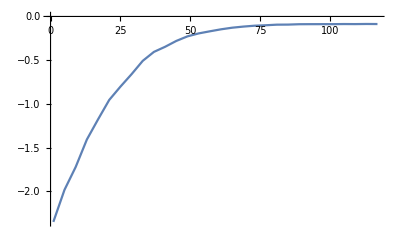

```mathematica
ListLinePlot[Table[{4*(i-1)+1,p3k3test[[i]]/10},{i,1,Length[p3k1test]}]]
```

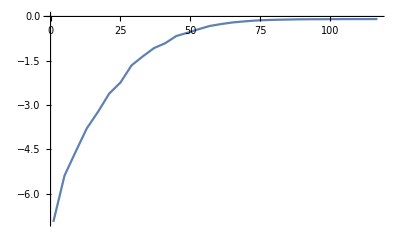

```mathematica
ListLinePlot[Table[{4*(i-1)+1,p3k5test[[i]]/10},{i,1,Length[p3k1test]}]]
```

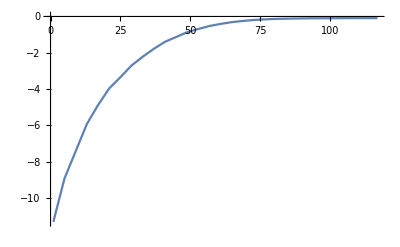

```mathematica
ListLinePlot[Table[{4*(i-1)+1,p3k7test[[i]]/10},{i,1,Length[p3k1test]}]]
```

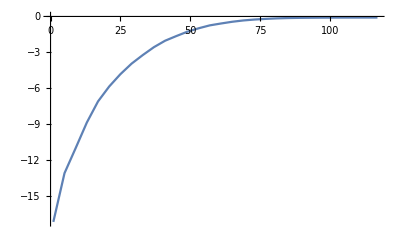

```mathematica
ListLinePlot[Table[{4*(i-1)+1,p3k9test[[i]]/10},{i,1,Length[p3k1test]}]]
```

```mathematica
(*testlogliks/16236*)
```

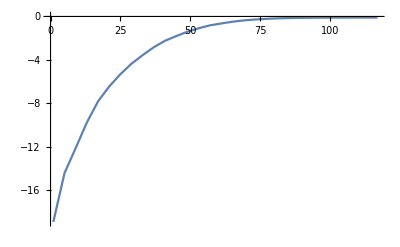

```mathematica
ListLinePlot[Table[{4*(i-1)+1,p3k10test[[i]]/10},{i,1,Length[p3k1test]}]]
```